## Bistability Analysis

```mathematica
(*Hill number 4*)
```

```mathematica
parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,n->4,ρ->9,α->100};
```

```mathematica
system={
m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/((p[t]*(ρ/((p[t]/α)-1)-1))+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
```

```mathematica
init={m[0]==.1,p[0]==.1};
```

```mathematica
fullsystem=Join[system,init];
```

```mathematica
numericsoln=NDSolve[fullsystem/.parameter,{m[t],p[t]},{t,0,2}]
```

{{m[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}}

```mathematica
(*solution plot(timecourse)*)
```

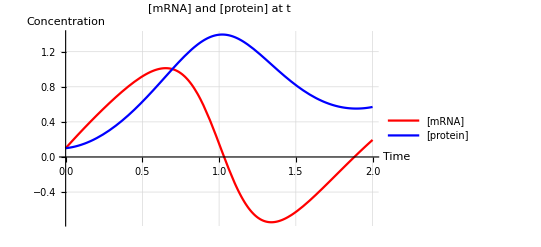

```mathematica
Plot[{{m[t]/.numericsoln},{p[t]/.numericsoln}},{t,0,2},PlotStyle->{{Red,Thick},{Blue, Thick}}, GridLines->Automatic,PlotRange->All, PlotLegends->{"[mRNA]","[protein]"},AxesLabel->{"Time","Concentration"},PlotLabel->"[mRNA] and [protein] at t"]
```

```mathematica
(*nullcline with vector fields*)
```

```mathematica
parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,n->4,ρ->9,α->100};
```

```mathematica
withpar1=Subscript[λ, m1]+Subscript[λ, m2]*p^n/((p*(ρ/((p/α)-1)-1))+p^n)-dm*m/.parameter
```

2-0.5 m+(18 p^4)/((-1+9/(-1+p/100)) p+p^4)

```mathematica
withpar2=λp*m-dp*p/.parameter
```

2 m-0.08 p

```mathematica
nullcline=Show[VectorPlot[{withpar1,withpar2},{m,-5,10},{p,-5,10},Epilog->{PointSize[0.03],Point[{m,p}/.First[Solve[withpar1==0,m],Solve[withpar2==0,p]]]},Frame->False,Axes->True],ContourPlot[{withpar1==0,withpar2==0},{m,-5,10},{p,-5,10},FrameLabel->{"mRNA","protein"}]]
```

-Graphics-

```mathematica
(*Streamplot*)
```

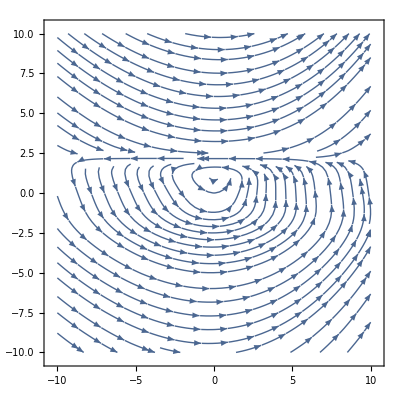

```mathematica
StreamPlot[{Subscript[λ, m1]+Subscript[λ, m2]*p^n/((p*(ρ/((p/α)-1)-1))+p^n)-dm*m,λp*m-dp*p}/.parameter,{m,-10,10},{p,-10,10}]
```

```mathematica
(*nullcline*)
```

```mathematica
parameter={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,n->4,ρ->9,α->100}
```

{λ_m1→2,λ_m2→18,dm→0.5,λp→2,dp→0.08,n→4,ρ→9,α→100}

```mathematica
f=Subscript[λ, m1]+Subscript[λ, m2]*p^n/((p*(ρ/((p/α)-1)-1))+p^n)-dm*m
```

-dm m+λ_m1+(p^n λ_m2)/(p^n+p (-1+ρ/(-1+p/α)))

```mathematica
g=λp*m-dp*p
```

-dp p+m λp

```mathematica
withpar1=f/.parameter
```

2-0.5 m+(18 p^4)/((-1+9/(-1+p/100)) p+p^4)

```mathematica
withpar2=g/.parameter
```

2 m-0.08 p

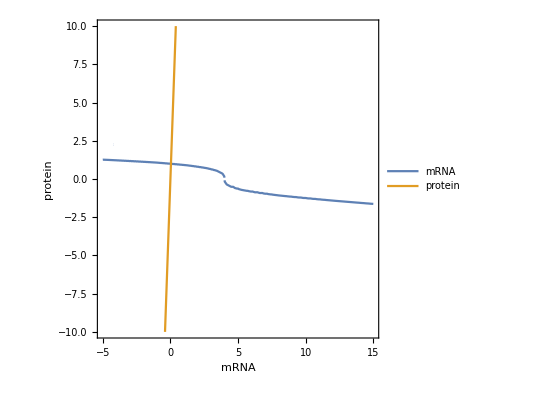

```mathematica
nullcline=ContourPlot[{withpar1==0,withpar2==0},{m,-5,15},{p,-10,10},FrameLabel->{"mRNA","protein"},PlotLegends->{"mRNA","protein"}]
```

```mathematica
(*Different Hill number*)
```

```mathematica
parameter1={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,k->.7,n->hillnum,ρ->9,α->100};
```

```mathematica
system1={
m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/((p[t]*(ρ/((p[t]/α)-1)-1))+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
```

```mathematica
init1={m[0]==.1,p[0]==.1};
```

```mathematica
fullsystem1=Join[system,init];
```

```mathematica
Manipulate[
parameter1={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,n->hillnum,ρ->9,α->100};
system1={
m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/((p[t]*(ρ/((p[t]/α)-1)-1))+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
init1={m[0]==.1,p[0]==.1};
fullsystem1=Join[system1,init1];
numericsoln1=NDSolve[fullsystem1/.parameter1,{m[t],p[t]},{t,0,10}];
Plot[Evaluate[{m[t],p[t]}/.numericsoln1,{t,0,10}],PlotStyle->{{Blue,Thick},{Orange,Thick, Dashed}},PlotRange->All,PlotLegends->{"mRNA","protein"},AxesLabel->{"time","mRNA protein"},PlotLabel->"mRNA and Protein"],
{{hillnum,1},0,10}]
```

NDSolve::ndsz: At t == 0.526632, step size is effectively zero; singularity or stiff system suspected.

```mathematica
α*(1+ρ)/.parameter
```

1000

```mathematica
ρ/.parameter
```

9

```mathematica
rhobound=(4*n)/(n-1)^2
```

(4 n)/(-1+n)^2

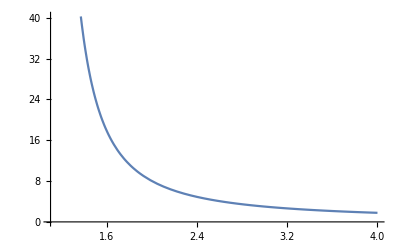

```mathematica
Plot[rhobound,{n,1.1,4}]
```

```mathematica
(*depends on k value*)
```

```mathematica
Manipulate[
parameter2={Subscript[λ, m1]->2,Subscript[λ, m2]->18,dm->0.5,λp->2,dp->0.08,n->4,k->kval};
system2={m'[t]==Subscript[λ, m1]+Subscript[λ, m2]*p[t]^n/(k^n+p[t]^n)-dm*m[t],
p'[t]==λp*m[t]-dp*p[t]};
init2={m[0]==3,p[0]==1};
fullsystem2=Join[system2,init2];
numericsoln2=NDSolve[fullsystem2/.parameter2,{m[t],p[t]},{t,0,10}];
Plot[Evaluate[{m[t],p[t]}/.numericsoln2,{t,0,10}],PlotStyle->{{Blue,Thick},{Orange,Thick, Dashed}},PlotRange->All,PlotLegends->{"mRNA","protein"},AxesLabel->{"time","mRNA protein"},PlotLabel->"mRNA and Protein"],
{{kval,1},0,100}]
```